```mathematica
dataaliceall = Import["/Users/guillaumepaya-monet/Documents/Projet Maths Music/coding/01_Midi_to_CSV/03_Clean_CSV_song_files/Boston_-_More_Than_A_Feeling.csv"];
```

```mathematica
CountLines[file_String/;FileExistsQ[file]]:=Module[{counter=0,str=OpenRead@file},While[Read[str,Record,NullRecords->True]=!=EndOfFile,counter++];
Close[str];
counter];
```

```mathematica
p=CountLines["/Users/guillaumepaya-monet/Documents/Projet Maths Music/coding/01_Midi_to_CSV/03_Clean_CSV_song_files/Boston_-_More_Than_A_Feeling.csv"];
```

```mathematica
pitch2=Flatten[dataaliceall[[2;;p,{7}]]];
```

```mathematica
f[a_,b_]:={Log[a],Log[b]}
```

```mathematica
data=KeyValueMap[f,Counts[pitch2]];
```

```mathematica
line=Fit[data,{1,x},x]
```

6.73652-0.421928 x

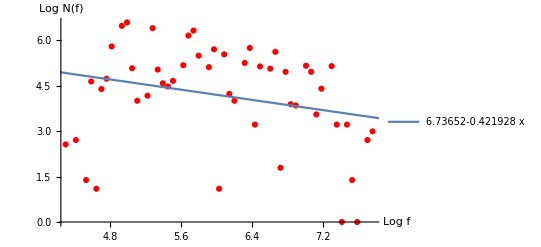

```mathematica
Show[ListPlot[data,PlotStyle->Red,AxesLabel->{"Log f","Log N(f)"}],Plot[{line},{x,0,10},PlotLegends->{line}]]
```